# Working Example for the SEM (Singular Euler-Maclaurin) Expansion

Andreas A. Buchheit and Torsten Keßler, 27.03.2020

The long-range elastic forces that act inside a one-dimensional crystal of macroscopic size are calculated using the SEM expansion.

## Parameter Settings

## Crystal Parameters

Scaling coefficient of interaction, only non-integer values. For integer values n,  take the limit ν0 -> n manually by adding an arbitrarily small offset.

```mathematica
ν0=1-10^(-10);
```

## Mathematica Settings

Parameter Assumptions

```mathematica
$Assumptions={x∈Reals,y∈Reals,λ>0,x∈Reals,0<δ≤1};
```

```mathematica
$MaxPiecewiseCases=5000;
```

```mathematica
Off[NIntegrate::nlim];
```

## Functions

## Interaction energy and forces

Interaction potential for x>0 (and V(-x)=V(x), where we avoid the use of Abs for performance reasons)

```mathematica
V[x_,ν_]=1/x^ν;
```

Normalised interaction potential

```mathematica
VNorm[x_,ν_]=V[x,ν]/(D[V[x,ν],{x,2}]/.{x->1})//FullSimplify;
```

Interaction force as a function of distance x for x>0. (sign is manually flipped for x<0)

```mathematica
ForceX[x_,ν_]=-D[VNorm[x,ν],x]//Simplify;
```

## Factorisation into s and g

```mathematica
s[y_]=Sign[y]ForceX[y,ν];
```

```mathematica
g[y_]=-ForceX[1+(u[x]-u[y])/(x-y),ν0];
```

## Kink interpolation function

```mathematica
Lorentzian[x_,λ_]=1/(Pi*λ)*λ^2/(x^2+λ^2);
```

```mathematica
Kink[y_,λ_]=Integrate[Lorentzian[x,λ],{x,-Infinity,y}];
```

## Singular Euler-Maclaurin Expansion

## SEM Generalised Bernoulli Functions

```mathematica
BernoulliA[x_,ν_,l_]:=Sum[Binomial[l,k]*(-1)^k*(HurwitzZeta[-k+ν,Ceiling[x]]*x^(l-k)-x^(l+1-ν)/(ν-k-1)),{k,0,l}];
```

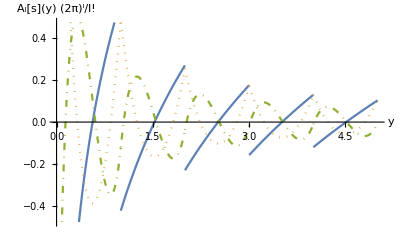

```mathematica
plotBernoulliA=Plot[{BernoulliA[x,ν0,0],2Pi*BernoulliA[x,ν0,1],(2Pi)^2/2!*BernoulliA[x,ν0,2]},{x,0,5},WorkingPrecision->50,ImageSize->Scaled[1/2],AxesLabel->{"y","A_l[s](y) (2π)^l/l!"},PlotPoints->200,PlotStyle->{Automatic,Dotted,DotDashed}]
```

## SEM Differential Operator Generation

Initialise SEM Operator for later use in the force functions

```mathematica
SEMOperatorGenerate[order_,nEdge_]:=Sum[(-1)^l*Derivative[l][g][nEdge+δ]*1/l!*BernoulliA[nEdge+δ-x,ν0+1,l]-(-1)^l*Derivative[l][g][x+δ]*1/l!*BernoulliA[δ,ν0+1,l],{l,0,order}]+Sum[Derivative[l][g][x-δ]*1/l!*BernoulliA[δ,ν0+1,l]-Derivative[l][g][-(nEdge+δ)]*1/l!*BernoulliA[nEdge+δ+x,ν0+1,l],{l,0,order}]/.u->(Kink[#,λ]&)
```

## SEM Force functions

```mathematica
ForceExact[x_,λ_,nEdge_]:=N[Sum[ForceX[x-y+Kink[x,λ]-Kink[y,λ],ν0],{y,-nEdge,x-1}]-Sum[ForceX[y-x+Kink[y,λ]-Kink[x,λ],ν0],{y,x+1,nEdge}],30];
```

```mathematica
ForceIntegralOnly[x_,λ_,δ_,nEdge_]=NIntegrate[ForceX[x-y+Kink[x,λ]-Kink[y,λ],ν0],{y,-nEdge-δ,x-δ},Method->"GlobalAdaptive",WorkingPrecision->30,PrecisionGoal->20,MaxRecursion->50,MinRecursion->2,AccuracyGoal->20]-NIntegrate[ForceX[y-x+Kink[y,λ]-Kink[x,λ],ν0],{y,x+δ,nEdge+δ},Method->"GlobalAdaptive",WorkingPrecision->30,PrecisionGoal->20,MaxRecursion->50,MinRecursion->2,AccuracyGoal->20];
```

```mathematica
(*ForceSEM[x_,λ_,δ_]=ForceIntegralOnly[x,λ,δ,nEdgeSpecific]-SEMOperatorGenerate[SEMOrder,nEdgeSpecific];*)
```

## Data Generation

## SEM and parameter settings

```mathematica
SEMOrder=1;
```

```mathematica
δ=1;
```

Set particle number and kink size.

```mathematica
nEdgeMacro=10^10;
λMacro=10^5;
```

```mathematica
nEdgeMicro=10^3;
λMicro=10^1;
```

## Generation of force functions

Generate SEM force functions

```mathematica
ForceSEMMacro[x_,λ_]=ForceIntegralOnly[x,λ,δ,nEdgeMacro]-SEMOperatorGenerate[SEMOrder,nEdgeMacro];
ForceSEMMicro[x_,λ_]=ForceIntegralOnly[x,λ,δ,nEdgeMicro]-SEMOperatorGenerate[SEMOrder,nEdgeMicro];
```

## Force tables for macroscopic and microscopic system

```mathematica
forceMacroRescaledTab=ParallelTable[{x/λMacro,λMacro^2ForceSEMMacro[x,λMacro]},{x,-3*λMacro,3*λMacro,Floor[1+λMacro/100]}];
forceIntegralOnlyMacroRescaledTab=ParallelTable[{x/λMacro,λMacro^2ForceIntegralOnly[x,λMacro,δ,nEdgeMacro]},{x,-3*λMacro,3*λMacro,Floor[1+λMacro/100]}];
```

```mathematica
forceMicroRescaledTab=ParallelTable[{x/λMicro,λMicro^2ForceSEMMicro[x,λMicro]},{x,-3*λMicro,3*λMicro,Floor[1+λMicro/100]}];
forceIntegralOnlyMicroRescaledTab=ParallelTable[{x/λMicro,λMicro^2ForceIntegralOnly[x,λMicro,δ,nEdgeMicro]},{x,-3*λMicro,3*λMicro,Floor[1+λMicro/100]}];
forceExactMicroRescaledTab=ParallelTable[{x/λMicro,λMicro^2ForceExact[x,λMicro,nEdgeMicro]},{x,-3*λMicro,3*λMicro,Floor[1+λMicro/100]}];
```

## Plots

Macroskopic system: λ = 10^5, N = 10^10

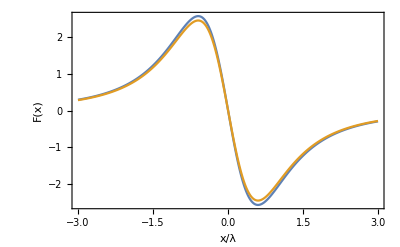

```mathematica
plotForceMacro=ListLinePlot[{forceMacroRescaledTab,forceIntegralOnlyMacroRescaledTab},Frame->True,ImageSize->Scaled[2/3],AxesLabel->{"x/λ","F(x)"}]
```

Microscopic system : λ = 10^1, N = 10^3

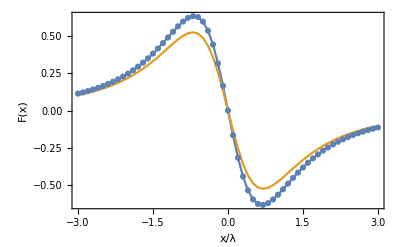

```mathematica
plotForceMicro=Show[ListLinePlot[{forceMicroRescaledTab,forceIntegralOnlyMicroRescaledTab},Frame->True,ImageSize->Scaled[2/3],AxesLabel->{"x/λ","F(x)"}],ListPlot[forceExactMicroRescaledTab]]
```

## Error scaling (Available if exact sums can still be computed)

## Error computation

Number of particles for error computation

```mathematica
nEdgeError=200;
```

Minimum and maximum value of λ for which the error is analysed over the whole crystal.

```mathematica
λmin=5;
λmax=25;
```

SEM orders to be investigated.

```mathematica
orderMin=-1;
orderMax=7;
orderIncrement=2;
```

Table of exact force arrays for values of λ incremented from λmin to λmax in steps of 1.

```mathematica
forceExactArray=Table[ParallelTable[{x,ForceExact[x,λ,nEdgeError]},{x,-nEdgeError,nEdgeError,1}],{λ,λmin,λmax}];
```

Generates Array with maximum error over the whole crystal for a specific SEM order. Requires forceExactArray.

```mathematica
GenerateMaxAbsErrorArray[order_]:=Module[{forceArray,absoluteErrorArray,ForceSEMLocal,maxAbsErrorArray},
If[order≥ 0,
ForceSEMLocal[x_,λ_,δ_]=ForceIntegralOnly[x,λ,δ,nEdgeError]-SEMOperatorGenerate[order,nEdgeError];,
ForceSEMLocal[x_,λ_,δ_]=ForceIntegralOnly[x,λ,δ,nEdgeError];]; 
forceArray=Table[ParallelTable[{x,ForceSEMLocal[x,λ,δ]},{x,-nEdgeError,nEdgeError,1}],{λ,λmin,λmax}];
absoluteErrorArray=Table[Transpose[{forceExactArray[[n]][[All,1]],(forceExactArray[[n]][[All,2]]-forceArray[[n]][[All,2]])}],{n,1,λmax-λmin+1}];
maxAbsErrorArray=Table[{λmin+n-1,Max[Abs[absoluteErrorArray[[n]][[All,2]]]]},{n,1, λmax-λmin+1} ];
Return[maxAbsErrorArray];
]
```

```mathematica
errorTab=Table[GenerateMaxAbsErrorArray[l],{l,orderMin,orderMax,orderIncrement}];
```

```mathematica
fitTab=Table[Exp[Fit[Take[Log[ errorTab[[l]] ],-5], {1,x},x]]/.{x->Log[y]}//Simplify,{l,1,Length[errorTab]}];
```

```mathematica
pLine=LogLogPlot[Evaluate[fitTab],{y,5,25},ImageSize->Scaled[2/3],PlotRange->{Automatic,{10^(-18),1+2}},AxesLabel->{"λ","maximum absolute error"}];
```

```mathematica
pError=ListLogLogPlot[errorTab,ImageSize->Scaled[2/3],PlotRange->{Automatic,{10^(-18),1+2}},AxesLabel->{"λ","maximum absolute error"}];
```

## Scaling plot

```mathematica
Show[pLine,pError]
```